```mathematica
hMean[x_,p0_,p1_,p2_,p3_]:= Exp[p1*x+p2*x^2+p3*x^3]+p0;
```

```mathematica
hMean1[x_,p0_,p1_,p2_]:= Log[p1*x+p2*x^2]+p0;
```

```mathematica
p0 = 3.55
 p1 =-1.2
 p2 = -0.2
p3 = -0.2
```

3.55

-1.2

-0.2

-0.2

```mathematica
3.55
```

3.5

```mathematica
hMean[4.0,p0,p1,p2,p3]
```

3.55

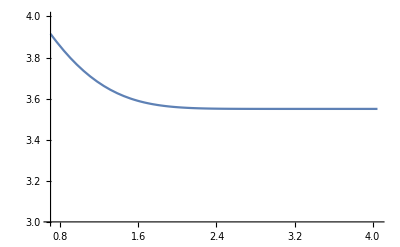

```mathematica
Plot[hMean[x,p0,p1,p2,p3],{x,0.7,4.05},PlotRange->{3,4}]
```

```mathematica
p01 = 0.03.5
 p11 =-1.2
 p21 = -0.2
```

3.5

-1.2

-0.2

```mathematica
Plot[hMean1[x,p01,p11,p21],{x,0.7,4.05},PlotRange->{3,4}]
```

-Graphics-

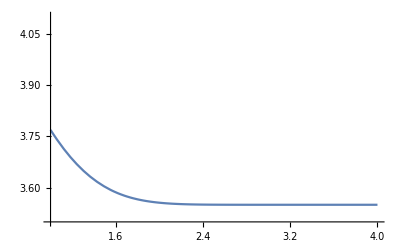

```mathematica
Plot[Exp[-x-0.3x^2-0.2x^3-0.02x^4]+3.55,{x,1.0,4},PlotRange->{3.5,4.1}]
```

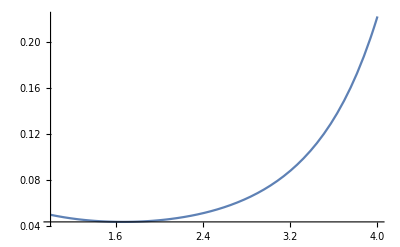

```mathematica
Plot[Exp[-x +0.3x^2]0.1,{x,1.0,4}]
```

```mathematica
Sigma[x_]= 0.1+0.1(0.01x +0.02x^2+0.01x^3);
```

```mathematica
Sigma[4.05]
```

0.203285

```mathematica
Plot0[0.0899+0.1(5.19287e-02x +1.72460e-02x^2+1.33058e-021x^3+3.03644e-04x^4+1.00006e-05x^5),{x,1.0,4}]
```

Plot0[0.0899+0.1 (12.2846 e-2 x-2 x^2-21 x^3-4 x^4-5 x^5),{x,1.,4}]

```mathematica
Plot[Exp[0.001x+0.003x^2+0.002x^3-0.02x^4]+3.55,{x,1.0,4},PlotRange->{3.5,4.1}]
```

-Graphics-